Листинг 2

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
Needs["FlowSolver`"]
```

```mathematica
readGraph2[file_,dir_]:=Module[{
	fn=FileNameJoin[{dir,file}],
	stream,imod,umod,u,b
	},
	stream=OpenRead[fn];
	imod=Read[stream,{Word,Number}][[2]];
	umod=Read[stream,{Word,Number}][[2]];
	u=({#_⟦1⟧->#_⟦2⟧,#_⟦2⟧->#_⟦1⟧}&/@ReadList[stream,Expression,umod])//Flatten;
b=ConstantArray[0,imod];
	(b[[Read[StringToStream[StringTake[#1,{5,-3}]],Number]]]=#2)&@@@ReadList[stream,{Word,Expression},imod];
{Graph[u,VertexSize->Medium,VertexLabels->Placed["Name",Center],VertexStyle->Directive[White], VertexShapeFunction->{xx_:> If[SameQ[b[[xx]],x],"Square","Circle"]},VertexLabelStyle->Directive[Black,24],GraphLayout->"CircularEmbedding"],b}]
```

```mathematica
forma[ff_]:=((ff/.{Subscript[ξ_, u_->v_]->Subscript[ξ, u,v]})//TableForm)
```

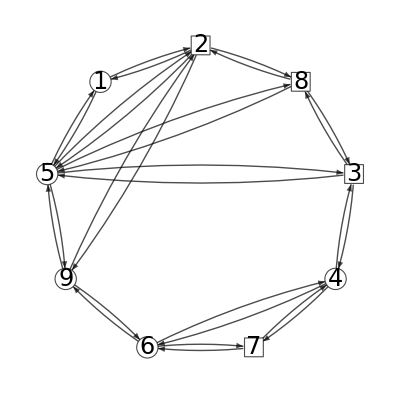

```mathematica
{g,b}=readGraph2["grDET0.txt",NotebookDirectory[]];
GraphPlot[g,EdgeStyle->Directive[Black,Thick], VertexStyle->Directive[EdgeForm[Thick],White],MultiedgeStyle->.05]
```

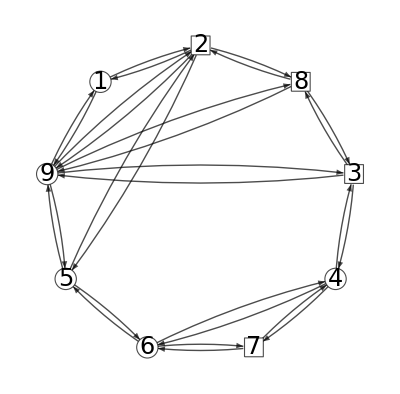

```mathematica
g=VertexReplace[g,{5->9,9->5}];
GraphPlot[g,EdgeStyle->Directive[Black,Thick], VertexStyle->Directive[EdgeForm[Thick],White],MultiedgeStyle->.05]
```

```mathematica
balanceEqs=((Total[Subscript[x, #]&/@EdgeList[g,_->#]]-Total[Subscript[x, #]&/@EdgeList[g,#->_]]))==MapIndexed[#1/.x->Subscript[x, #2[[1]]]&,b][[#]]&/@VertexList[g];
balanceEqs//forma
```

-x_(1,2)-x_(1,9)+x_(2,1)+x_(9,1)==0
x_(1,2)-x_(2,1)-x_(2,5)-x_(2,8)-x_(2,9)+x_(5,2)+x_(8,2)+x_(9,2)==x_2
x_(1,9)+x_(2,9)+x_(3,9)+x_(5,9)+x_(8,9)-x_(9,1)-x_(9,2)-x_(9,3)-x_(9,5)-x_(9,8)==0
x_(2,8)+x_(3,8)-x_(8,2)-x_(8,3)-x_(8,9)+x_(9,8)==x_8
-x_(3,4)-x_(3,8)-x_(3,9)+x_(4,3)+x_(8,3)+x_(9,3)==x_3
x_(3,4)-x_(4,3)-x_(4,6)-x_(4,7)+x_(6,4)+x_(7,4)==0
x_(4,7)+x_(6,7)-x_(7,4)-x_(7,6)==x_7
x_(4,6)+x_(5,6)-x_(6,4)-x_(6,5)-x_(6,7)+x_(7,6)==0
x_(2,5)-x_(5,2)-x_(5,6)-x_(5,9)+x_(6,5)+x_(9,5)==0

```mathematica
M={9};
Print["M = ", M];
```

M = {9}

```mathematica
(*Do[inclist=EdgeList[g,u->_];Do[Subscript[p, v]=1/Length[inclist];,{v,inclist}];,{u,VertexList[g]}]*)
```

```mathematica
(*Subscript[p, #]&/@EdgeList[g]*)
```

```mathematica
(*incL=DeleteCases[DeleteDuplicates[Cases[IncidenceList[g,#],i_->j_:>{i,j}]//Flatten],v_/;v==#]&/@M*)
incL=(IncidenceList[g,#]&/@M)//Flatten
```

{1->9,9->1,8->9,9->8,2->9,9->2,5->9,9->5,3->9,9->3}

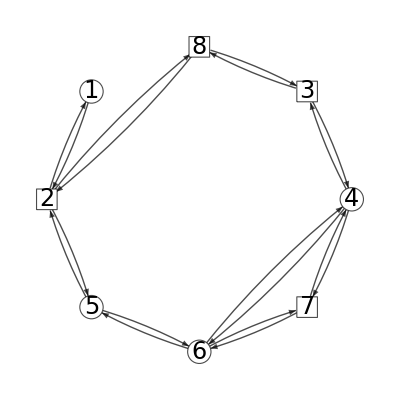

{f_(1->9)-f_(9->1),x+f_(2->9)-f_(9->2),x+f_(3->9)-f_(9->3),0,f_(5->9)-f_(9->5),0,x,x+f_(8->9)-f_(9->8)}

```mathematica
(*Do[If[MemberQ[M,j_⟦1⟧],b_⟦j⟦2⟧⟧+=Subscript[f, j],b_⟦j⟦1⟧⟧-=Subscript[f, j]],{j,incL}]*)
b̄=Fold[If[MemberQ[M,#2_⟦1⟧],ReplacePart[#,#2_⟦2⟧->#_⟦#2⟦2⟧⟧-Subscript[f, #2]],ReplacePart[#,#2_⟦1⟧->#_⟦#2⟦1⟧⟧+Subscript[f, #2]]]&,b,incL];
b̄=b̄[[Range[g//VertexCount]~Complement~M]];
OverBar[ng]=VertexDelete[g,M];
GraphPlot[OverBar[ng],EdgeStyle->Directive[Black,Thick], VertexStyle->Directive[EdgeForm[Thick],White],MultiedgeStyle->.05]
b̄
```

```mathematica
CC[g_,M_]:=(DeleteDuplicates[Cases[IncidenceList[g,#],i_->j_/;j==#]]&/@M)//Flatten

SuperPlus[Subscript[ii, i_]][g_]:=Cases[IncidenceList[g,i],u_->v_/;u==i:>v]
```

```mathematica
SuperPlus[M]=CC[g,M]
```

{1->9,8->9,2->9,5->9,3->9}

```mathematica
OverBar[b1]=Fold[Module[{bb=#1,i=#2_[[1]],k=#2_[[2]]},(Fold[Module[{bbb=#1,jj=#2},ReplacePart[bbb, ((({jj->bbb_⟦jj⟧-Subscript[p, i->jj]/Subscript[p, i->k] Subscript[f, i->k],i->bbb_⟦i⟧+Subscript[p, i->jj]/Subscript[p, i->k] Subscript[f, i->k]})))//Flatten]]&,bb,SuperPlus[Subscript[ii, i]][OverBar[ng]]])]&,b̄,SuperPlus[M]]
```

{f_(1->9)-f_(9->1)+(f_(1->9) p_(1->2))/(p_(1->9))-(f_(2->9) p_(2->1))/(p_(2->9)),x+f_(2->9)-f_(9->2)-(f_(1->9) p_(1->2))/(p_(1->9))+(f_(2->9) p_(2->1))/(p_(2->9))+(f_(2->9) p_(2->5))/(p_(2->9))+(f_(2->9) p_(2->8))/(p_(2->9))-(f_(5->9) p_(5->2))/(p_(5->9))-(f_(8->9) p_(8->2))/(p_(8->9)),x+f_(3->9)-f_(9->3)+(f_(3->9) p_(3->4))/(p_(3->9))+(f_(3->9) p_(3->8))/(p_(3->9))-(f_(8->9) p_(8->3))/(p_(8->9)),-(f_(3->9) p_(3->4))/(p_(3->9)),f_(5->9)-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) p_(5->2))/(p_(5->9))+(f_(5->9) p_(5->6))/(p_(5->9)),-(f_(5->9) p_(5->6))/(p_(5->9)),x,x+f_(8->9)-f_(9->8)-(f_(2->9) p_(2->8))/(p_(2->9))-(f_(3->9) p_(3->8))/(p_(3->9))+(f_(8->9) p_(8->2))/(p_(8->9))+(f_(8->9) p_(8->3))/(p_(8->9))}

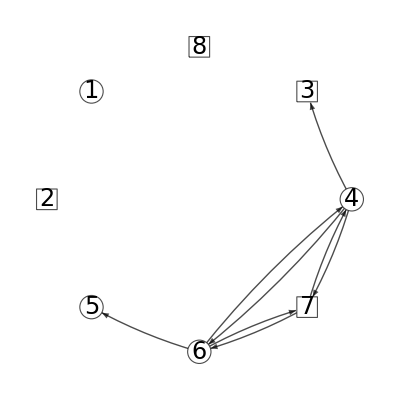

```mathematica
GraphPlot[Fold[HighlightGraph[#1,u_->v_/;u==#2, GraphHighlightStyle->"White"]&,OverBar[ng],#_[[1]]&/@SuperPlus[M]],EdgeStyle->Directive[Black,Thick], VertexStyle->Directive[EdgeForm[Thick],White],MultiedgeStyle->.05]
```

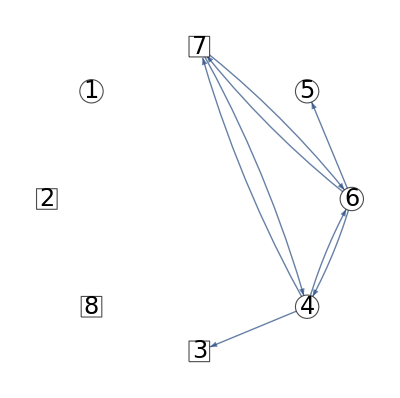

```mathematica
OverBar[g1]=Fold[EdgeDelete[#1,u_->v_/;u==#2]&,OverBar[ng],#_[[1]]&/@SuperPlus[M]];
GraphPlot[OverBar[g1],MultiedgeStyle->.05]
```

```mathematica
Subscript[II, rem]=VertexList[OverBar[g1]]~Complement~(SuperPlus[M]⟦All,1⟧)
```

{4,6,7}

```mathematica
λ=SparseArray[Replace[(EdgeList[OverBar[g1]]/.#&/@Flatten[Module[{i=#,jf,Icur},(Icur=SuperPlus[Subscript[ii, i]][OverBar[g1]];jf=First[Icur];({(i->jf)->1,(i->#)->- Subscript[p, i->#]/Subscript[p, i->jf]})&/@Icur⟦2;;⟧)]&/@Subscript[II, rem],1]),_->_->0,2]]
```

SparseArray[…]

```mathematica
Grid[λ]
```

1 | -(p_(4->7))/(p_(4->3)) | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | -(p_(4->6))/(p_(4->3)) | 0
0 | 0 | 0 | 0 | 1 | -(p_(6->4))/(p_(6->7)) | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -(p_(6->5))/(p_(6->7))
0 | 0 | 1 | -(p_(7->6))/(p_(7->4)) | 0 | 0 | 0 | 0

```mathematica
g=OverBar[g1];
b=OverBar[b1];
```

```mathematica
SuperStar[II]=Cases[MapIndexed[{#1,#2}&,b],{el_,i_}/;MemberQ[el,x]||SameQ[el,x]:>i]//Flatten
```

{2,3,7,8}

```mathematica
buildt=Timing[{t,g}=buildTree[g,SuperStar[II]];][[1]]
TableForm[t⟦1;;4⟧,TableHeadings->{{"pred","dir","depth","d"},t//pred//Length//Range}]
```

0.

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
pred | 0 | 9 | 9 | 3 | 6 | 7 | 9 | 9 | 0
dir | 0 | 1 | 1 | -1 | 1 | 1 | 1 | 1 | 0
depth | 0 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 0
d | 9 | 8 | 4 | 7 | 9 | 5 | 6 | 3 | 2

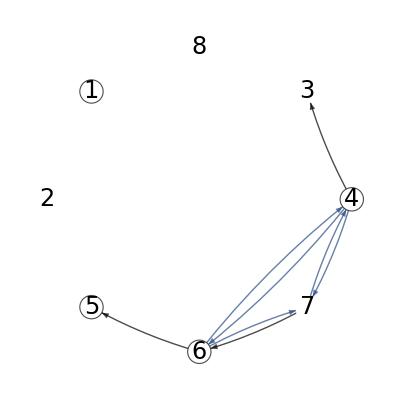

```mathematica
GraphPlot[HighlightGraph[Fold[HighlightGraph[#1,Style[u_->v_/;u==#2,White]]&,OverBar[ng],#_[[1]]&/@SuperPlus[M]],{Style[u_/;VertexQ[g,u]&&pred[t][[u]]==root[t],EdgeForm[Thick]],Style[u_->v_/;(pred[t][[u]]==v&&dir[t][[u]]==-1)||(pred[t][[v]]==u&&dir[t][[v]]==1),Directive[Black,Thick]]},GraphHighlightStyle->None],MultiedgeStyle->.05]
```

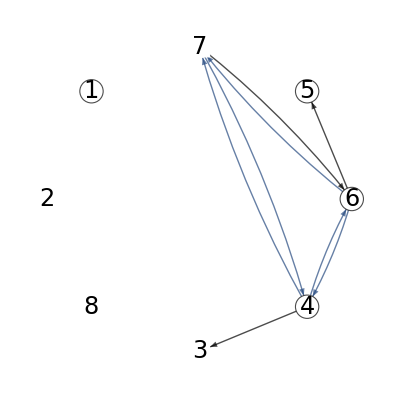

```mathematica
GraphPlot[HighlightGraph[OverBar[g1],{Style[u_/;VertexQ[g,u]&&pred[t][[u]]==root[t],EdgeForm[Thick]],Style[u_->v_/;(pred[t][[u]]==v&&dir[t][[u]]==-1)||(pred[t][[v]]==u&&dir[t][[v]]==1),Directive[Black,Thick]]},GraphHighlightStyle->None],MultiedgeStyle->.05]
```

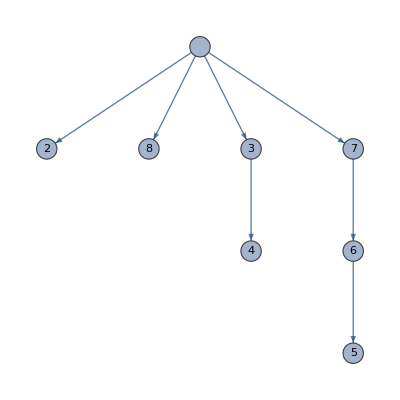

```mathematica
t[[7]](*пометить на графе*)
```

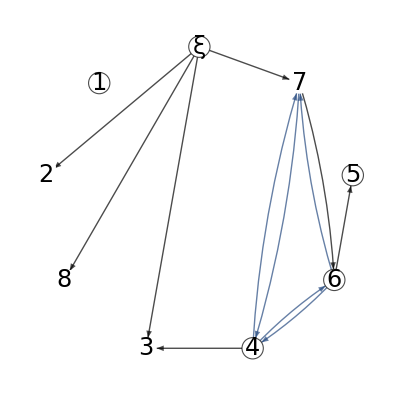

```mathematica
(*GraphPlot[g,MultiedgeStyle->.05]*)
GraphPlot[HighlightGraph[g,{Style[u_/;VertexQ[g,u]&&pred[t][[u]]==root[t],EdgeForm[Thick]],Style[u_->v_/;(pred[t][[u]]==v&&dir[t][[u]]==-1)||(pred[t][[v]]==u&&dir[t][[v]]==1),Directive[Black,Thick]]},GraphHighlightStyle->None],MultiedgeStyle->.05]
```

```mathematica
AppendTo[b,-Total[b]];
b=Simplify[b/.x->0]
```

{-f_(9->1)+f_(1->9) (1+(p_(1->2))/(p_(1->9)))-(f_(2->9) p_(2->1))/(p_(2->9)),-f_(9->2)-(f_(1->9) p_(1->2))/(p_(1->9))+(f_(2->9) (p_(2->1)+p_(2->5)+p_(2->8)+p_(2->9)))/(p_(2->9))-(f_(5->9) p_(5->2))/(p_(5->9))-(f_(8->9) p_(8->2))/(p_(8->9)),-f_(9->3)+(f_(3->9) (p_(3->4)+p_(3->8)+p_(3->9)))/(p_(3->9))-(f_(8->9) p_(8->3))/(p_(8->9)),-(f_(3->9) p_(3->4))/(p_(3->9)),-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9)),-(f_(5->9) p_(5->6))/(p_(5->9)),0,-f_(9->8)-(f_(2->9) p_(2->8))/(p_(2->9))-(f_(3->9) p_(3->8))/(p_(3->9))+(f_(8->9) (p_(8->2)+p_(8->3)+p_(8->9)))/(p_(8->9)),-f_(1->9)-f_(2->9)-f_(3->9)-f_(5->9)-f_(8->9)+f_(9->1)+f_(9->2)+f_(9->3)+f_(9->5)+f_(9->8)}

```mathematica
balanceEqs=((Total[Subscript[x, #]&/@EdgeList[g,_->#]]-Total[Subscript[x, #]&/@EdgeList[g,#->_]])/. root[t]->ξ)==b[[#]]&/@VertexList[g];
balanceEqs//forma
```

0==-f_(9,1)+f_(1,9) (1+(p_(1,2))/(p_(1,9)))-(f_(2,9) p_(2,1))/(p_(2,9))
x_(ξ,2)==-f_(9,2)-(f_(1,9) p_(1,2))/(p_(1,9))+(f_(2,9) (p_(2,1)+p_(2,5)+p_(2,8)+p_(2,9)))/(p_(2,9))-(f_(5,9) p_(5,2))/(p_(5,9))-(f_(8,9) p_(8,2))/(p_(8,9))
x_(ξ,8)==-f_(9,8)-(f_(2,9) p_(2,8))/(p_(2,9))-(f_(3,9) p_(3,8))/(p_(3,9))+(f_(8,9) (p_(8,2)+p_(8,3)+p_(8,9)))/(p_(8,9))
x_(4,3)+x_(ξ,3)==-f_(9,3)+(f_(3,9) (p_(3,4)+p_(3,8)+p_(3,9)))/(p_(3,9))-(f_(8,9) p_(8,3))/(p_(8,9))
-x_(4,3)-x_(4,6)-x_(4,7)+x_(6,4)+x_(7,4)==-(f_(3,9) p_(3,4))/(p_(3,9))
x_(4,7)+x_(6,7)-x_(7,4)-x_(7,6)+x_(ξ,7)==0
x_(4,6)-x_(6,4)-x_(6,5)-x_(6,7)+x_(7,6)==-(f_(5,9) p_(5,6))/(p_(5,9))
x_(6,5)==-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))
-x_(ξ,2)-x_(ξ,3)-x_(ξ,7)-x_(ξ,8)==-f_(1,9)-f_(2,9)-f_(3,9)-f_(5,9)-f_(8,9)+f_(9,1)+f_(9,2)+f_(9,3)+f_(9,5)+f_(9,8)

```mathematica
ps=partSolve[g,-b,t,x̃];
ps//forma
```

(x̃)_(4,3)→(f_(3,9) p_(3,4))/(p_(3,9))
(x̃)_(4,6)→0
(x̃)_(4,7)→0
(x̃)_(6,4)→0
(x̃)_(6,5)→-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))
(x̃)_(6,7)→0
(x̃)_(7,4)→0
(x̃)_(7,6)→-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))-(f_(5,9) p_(5,6))/(p_(5,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))
(x̃)_(9,2)→-f_(9,2)-(f_(1,9) p_(1,2))/(p_(1,9))+(f_(2,9) (p_(2,1)+p_(2,5)+p_(2,8)+p_(2,9)))/(p_(2,9))-(f_(5,9) p_(5,2))/(p_(5,9))-(f_(8,9) p_(8,2))/(p_(8,9))
(x̃)_(9,3)→-f_(9,3)-(f_(3,9) p_(3,4))/(p_(3,9))+(f_(3,9) (p_(3,4)+p_(3,8)+p_(3,9)))/(p_(3,9))-(f_(8,9) p_(8,3))/(p_(8,9))
(x̃)_(9,7)→-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))-(f_(5,9) p_(5,6))/(p_(5,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))
(x̃)_(9,8)→-f_(9,8)-(f_(2,9) p_(2,8))/(p_(2,9))-(f_(3,9) p_(3,8))/(p_(3,9))+(f_(8,9) (p_(8,2)+p_(8,3)+p_(8,9)))/(p_(8,9))
(x̃)_(1<->0)→0

```mathematica
Simplify[(balanceEqs/.{x->x̃,ξ->root[t]})/.ps]
```

{f_(9->1)+(f_(2->9) p_(2->1))/(p_(2->9))==f_(1->9) (1+(p_(1->2))/(p_(1->9))),True,True,True,True,True,True,True,f_(9->1)+f_(1->9) (-1-(p_(1->2))/(p_(1->9)))+(f_(2->9) p_(2->1))/(p_(2->9))==0}

```mathematica
matrt=Timing[δMatr=δ1[g,t]];
roott=VertexCount[g];
TableForm[δMatr,TableHeadings->{uNb[g,t],Subscript[δ, Piecewise[{{#_⟦2⟧, #_⟦1⟧== roott}, {#_⟦1⟧, #⟦2⟧==roott}, {#, True}}]]&/@EdgeList[g]}]//forma
```

| δ_(4,3) | δ_(4,7) | δ_(7,4) | δ_(7,6) | δ_(6,7) | δ_(6,4) | δ_(4,6) | δ_(6,5) | δ_2 | δ_3 | δ_7 | δ_8
4->7 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0
7->4 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
6->7 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6->4 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 0
4->6 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 0

```mathematica
λ=SparseArray[λ,{Length[λ],Length[λ[[1]]]+Length[SuperStar[II]]}];
(*λ=λ[[;;-2]]*)
```

```mathematica
dopEq=#==0&/@Flatten[λ.Transpose[{Subscript[x, #]&/@EdgeList[g]}]];
dopEq//forma
```

x_(4,3)-(p_(4,7) x_(4,7))/(p_(4,3))==0
x_(4,3)-(p_(4,6) x_(4,6))/(p_(4,3))==0
-(p_(6,4) x_(6,4))/(p_(6,7))+x_(6,7)==0
-(p_(6,5) x_(6,5))/(p_(6,7))+x_(6,7)==0
x_(7,4)-(p_(7,6) x_(7,6))/(p_(7,4))==0

```mathematica
Λ=λ.Transpose[(δMatr)];
"cicle det's:"
Λ//forma
```

cicle det's:

-1-(p_(4->7))/(p_(4->3)) | 1 | 0 | 1 | -1
-1 | 1 | 0 | 1 | -1-(p_(4->6))/(p_(4->3))
0 | 0 | 1 | -(p_(6->4))/(p_(6->7)) | 0
0 | 0 | 1 | 0 | 0
0 | 1 | -(p_(7->6))/(p_(7->4)) | -(p_(7->6))/(p_(7->4)) | (p_(7->6))/(p_(7->4))

```mathematica
rank=MatrixRank[Λ]
```

5

```mathematica
"U_c="
Subscript[U, c]=Range[rank]
"U_nc="
Subscript[U, nc]=Range[Length[Λ[[1]]]]~Complement~Subscript[U, c]
```

U_c=

{1,2,3,4,5}

U_nc=

{}

```mathematica
Λc=Λ[[All,Subscript[U, c]]];
Λnc=Λ[[All,Subscript[U, nc]]];
"Λ_c="
Λc//MatrixForm
```

Λ_c=

(-1-(p_(4->7))/(p_(4->3)) | 1 | 0 | 1 | -1
-1 | 1 | 0 | 1 | -1-(p_(4->6))/(p_(4->3))
0 | 0 | 1 | -(p_(6->4))/(p_(6->7)) | 0
0 | 0 | 1 | 0 | 0
0 | 1 | -(p_(7->6))/(p_(7->4)) | -(p_(7->6))/(p_(7->4)) | (p_(7->6))/(p_(7->4)))

```mathematica
"det(Λ_c)="
Simplify[det=Det[Λc]]//forma
```

det(Λ_c)=

-(p_(6,4) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))))/(p_(4,3)^2 p_(6,7) p_(7,4))

```mathematica
"U_T="
utind=Cases[t[[6]],ξ_/;ξ≠0];
Subscript[U, T]=EdgeList[g][[utind]]
```

U_T=

{9->2,9->3,4->3,6->5,7->6,9->7,9->8}

```mathematica
"U_Nb="
Subscript[U, Nb]=uNb[g,t]
```

U_Nb=

{4->7,7->4,6->7,6->4,4->6}

```mathematica
A=-λ.Transpose[{Subscript[x̃, #]&/@EdgeList[g]}]/.ps;
"A="
A//MatrixForm
```

A=

(-(f_(3->9) p_(3->4))/(p_(3->9))
-(f_(3->9) p_(3->4))/(p_(3->9))
0
((-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(6->5))/(p_(6->7))
((-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))-(f_(5->9) p_(5->6))/(p_(5->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(7->6))/(p_(7->4)))

```mathematica
β=A(*-Λnc.{Subscript[x, #]&/@Subscript[U, Nb][[Subscript[U, nc]]]}^ᵀ*);
"β="
β//forma
```

β=

-(f_(3,9) p_(3,4))/(p_(3,9))
-(f_(3,9) p_(3,4))/(p_(3,9))
0
((-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))) p_(6,5))/(p_(6,7))
((-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))-(f_(5,9) p_(5,6))/(p_(5,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))) p_(7,6))/(p_(7,4))

```mathematica
"решаем уравнение Λ_cx_c=β:"
xc=LinearSolve[Λc,β[[]]]
```

решаем уравнение Λ_cx_c=β:

{{(f_(3->9) p_(2->9) p_(3->4) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7) p_(7->4)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->5) p_(6->7) p_(7->4)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->5) p_(6->7) p_(7->4)-f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->4)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->4)-f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->4)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->4) p_(6->5) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->4) p_(6->5) p_(7->6)-f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5) p_(7->6)-f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->4) p_(6->7) p_(7->6)-f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7) p_(7->6)-f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->5) p_(6->7) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->5) p_(6->7) p_(7->6)-f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->6)-f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->6))/(p_(2->9) p_(3->9) p_(5->9) p_(6->4) p_(6->7) (p_(4->3) p_(4->6) p_(7->4)+p_(4->3) p_(4->7) p_(7->4)+p_(4->6) p_(4->7) p_(7->4)+p_(4->3) p_(4->7) p_(7->6)))},{-(((-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->2) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->2) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->6) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->6) p_(6->4) p_(6->5)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->5)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->5)+f_(2->9) p_(2->5) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->5)+f_(9->5) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->2) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->2) p_(6->4) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7)+f_(3->9) p_(2->9) p_(3->4) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->2) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->6) p_(6->5) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->5) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->5) p_(6->7)) p_(7->6))/(p_(2->9) p_(3->9) p_(5->9) p_(6->4) p_(6->7) (p_(4->3) p_(4->6) p_(7->4)+p_(4->3) p_(4->7) p_(7->4)+p_(4->6) p_(4->7) p_(7->4)+p_(4->3) p_(4->7) p_(7->6))))},{((-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(6->5))/(p_(6->7))},{((-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(6->5))/(p_(6->4))},{(p_(6->7) ((p_(6->4) ((f_(3->9) p_(3->4))/(p_(3->9))+(f_(3->9) p_(3->4) (-1-(p_(4->7))/(p_(4->3))))/(p_(3->9))-(p_(4->7) (-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))-(f_(5->9) p_(5->6))/(p_(5->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(7->6))/(p_(4->3) p_(7->4))))/(p_(6->7))-((-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(6->5) ((p_(4->7))/(p_(4->3))+(p_(4->7) p_(7->6))/(p_(4->3) p_(7->4))+(p_(4->7) p_(6->4) p_(7->6))/(p_(4->3) p_(6->7) p_(7->4))))/(p_(6->7))))/(p_(6->4) (1-(-1-(p_(4->6))/(p_(4->3))) (-1-(p_(4->7))/(p_(4->3)))-(p_(4->7) p_(7->6))/(p_(4->3) p_(7->4))))}}

```mathematica
xcp=MapThread[Subscript[x, #1]->#2&,{Subscript[U, Nb][[Subscript[U, c]]],Flatten[xc]}];
xcp//TableForm
```

x_(4->7)→(f_(3->9) p_(2->9) p_(3->4) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7) p_(7->4)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->5) p_(6->7) p_(7->4)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->5) p_(6->7) p_(7->4)-f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->4)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->4)-f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->4)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->4) p_(6->5) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->4) p_(6->5) p_(7->6)-f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5) p_(7->6)-f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->4) p_(6->7) p_(7->6)-f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7) p_(7->6)-f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->5) p_(6->7) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->5) p_(6->7) p_(7->6)-f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->6)+f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->6)-f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7) p_(7->6))/(p_(2->9) p_(3->9) p_(5->9) p_(6->4) p_(6->7) (p_(4->3) p_(4->6) p_(7->4)+p_(4->3) p_(4->7) p_(7->4)+p_(4->6) p_(4->7) p_(7->4)+p_(4->3) p_(4->7) p_(7->6)))
x_(7->4)→-((-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->2) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->2) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->6) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->6) p_(6->4) p_(6->5)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->5)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->5)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->5)+f_(2->9) p_(2->5) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->5)+f_(9->5) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->5)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->2) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->2) p_(6->4) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->4) p_(6->7)+f_(3->9) p_(2->9) p_(3->4) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->7) p_(5->9) p_(6->4) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->4) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->2) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->2) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->6) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->6) p_(6->5) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->3) p_(4->6) p_(5->9) p_(6->5) p_(6->7)+f_(2->9) p_(2->5) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->5) p_(6->7)-f_(5->9) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->5) p_(6->7)+f_(9->5) p_(2->9) p_(3->9) p_(4->6) p_(4->7) p_(5->9) p_(6->5) p_(6->7)) p_(7->6))/(p_(2->9) p_(3->9) p_(5->9) p_(6->4) p_(6->7) (p_(4->3) p_(4->6) p_(7->4)+p_(4->3) p_(4->7) p_(7->4)+p_(4->6) p_(4->7) p_(7->4)+p_(4->3) p_(4->7) p_(7->6)))
x_(6->7)→((-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(6->5))/(p_(6->7))
x_(6->4)→((-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(6->5))/(p_(6->4))
x_(4->6)→(p_(6->7) ((p_(6->4) ((f_(3->9) p_(3->4))/(p_(3->9))+(f_(3->9) p_(3->4) (-1-(p_(4->7))/(p_(4->3))))/(p_(3->9))-(p_(4->7) (-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))-(f_(5->9) p_(5->6))/(p_(5->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(7->6))/(p_(4->3) p_(7->4))))/(p_(6->7))-((-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))) p_(6->5) ((p_(4->7))/(p_(4->3))+(p_(4->7) p_(7->6))/(p_(4->3) p_(7->4))+(p_(4->7) p_(6->4) p_(7->6))/(p_(4->3) p_(6->7) p_(7->4))))/(p_(6->7))))/(p_(6->4) (1-(-1-(p_(4->6))/(p_(4->3))) (-1-(p_(4->7))/(p_(4->3)))-(p_(4->7) p_(7->6))/(p_(4->3) p_(7->4))))

```mathematica
s=solveAll[g,t];
s//TableForm
```

x_(4->3)→(f_(3->9) p_(3->4))/(p_(3->9))-x_(4->6)-x_(4->7)+x_(6->4)+x_(7->4)
x_(7->6)→-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))-(f_(5->9) p_(5->6))/(p_(5->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))-x_(4->6)+x_(6->4)+x_(6->7)
x_(6->5)→-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))
x_(9->2)→-f_(9->2)-(f_(1->9) p_(1->2))/(p_(1->9))+(f_(2->9) (p_(2->1)+p_(2->5)+p_(2->8)+p_(2->9)))/(p_(2->9))-(f_(5->9) p_(5->2))/(p_(5->9))-(f_(8->9) p_(8->2))/(p_(8->9))
x_(9->3)→-f_(9->3)-(f_(3->9) p_(3->4))/(p_(3->9))+(f_(3->9) (p_(3->4)+p_(3->8)+p_(3->9)))/(p_(3->9))-(f_(8->9) p_(8->3))/(p_(8->9))+x_(4->6)+x_(4->7)-x_(6->4)-x_(7->4)
x_(9->7)→-f_(9->5)-(f_(2->9) p_(2->5))/(p_(2->9))-(f_(5->9) p_(5->6))/(p_(5->9))+(f_(5->9) (p_(5->2)+p_(5->6)+p_(5->9)))/(p_(5->9))-x_(4->6)-x_(4->7)+x_(6->4)+x_(7->4)
x_(9->8)→-f_(9->8)-(f_(2->9) p_(2->8))/(p_(2->9))-(f_(3->9) p_(3->8))/(p_(3->9))+(f_(8->9) (p_(8->2)+p_(8->3)+p_(8->9)))/(p_(8->9))

```mathematica
"общее решение:"
xsol=((s/.xcp)~Join~xcp);
xsol/.{Subscript[ξ_, u_->v_]->Subscript[ξ, u,v]}//Simplify//TableForm
```

общее решение:

x_(4,3)→(p_(4,6) p_(4,7) (f_(3,9) p_(2,9) p_(3,4) p_(5,9) p_(6,4) p_(6,7) p_(7,4)+p_(3,9) (-(f_(2,9) p_(2,5)+f_(9,5) p_(2,9)) p_(5,9) (p_(6,4) p_(6,7) p_(7,6)+p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))+f_(5,9) p_(2,9) (p_(5,6) p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6)))+p_(5,2) (p_(6,4) p_(6,7) p_(7,6)+p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))+p_(5,9) (p_(6,4) p_(6,7) p_(7,6)+p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))))))/(p_(2,9) p_(3,9) p_(5,9) p_(6,4) p_(6,7) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))))
x_(7,6)→-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))-(f_(5,9) p_(5,6))/(p_(5,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))+((-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))) p_(6,5))/(p_(6,4))+((-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))) p_(6,5))/(p_(6,7))+(p_(4,3) p_(4,7) (-(p_(6,4) (f_(3,9) p_(2,9) p_(3,4) p_(5,9) p_(7,4)+p_(3,9) (-(f_(2,9) p_(2,5)+f_(9,5) p_(2,9)) p_(5,9)+f_(5,9) p_(2,9) (p_(5,2)+p_(5,9))) p_(7,6)))/(p_(3,9))-((-(f_(2,9) p_(2,5)+f_(9,5) p_(2,9)) p_(5,9)+f_(5,9) p_(2,9) (p_(5,2)+p_(5,6)+p_(5,9))) p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))/(p_(6,7))))/(p_(2,9) p_(5,9) p_(6,4) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))))
x_(6,5)→-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))
x_(9,2)→-f_(9,2)-(f_(1,9) p_(1,2))/(p_(1,9))+(f_(2,9) (p_(2,1)+p_(2,5)+p_(2,8)+p_(2,9)))/(p_(2,9))-(f_(5,9) p_(5,2))/(p_(5,9))-(f_(8,9) p_(8,2))/(p_(8,9))
x_(9,3)→(f_(3,9) p_(2,9) p_(5,9) p_(6,4) p_(6,7) (p_(3,4) p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))+(p_(3,8)+p_(3,9)) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))))-p_(3,9) (f_(9,3) p_(2,9) p_(5,9) p_(6,4) p_(6,7) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6))))+p_(4,6) p_(4,7) (-(f_(2,9) p_(2,5)+f_(9,5) p_(2,9)) p_(5,9) (p_(6,4) p_(6,7) p_(7,6)+p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))+f_(5,9) p_(2,9) (p_(5,6) p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6)))+p_(5,2) (p_(6,4) p_(6,7) p_(7,6)+p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))+p_(5,9) (p_(6,4) p_(6,7) p_(7,6)+p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))))))/(p_(2,9) p_(3,9) p_(5,9) p_(6,4) p_(6,7) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))))-(f_(8,9) p_(8,3))/(p_(8,9))
x_(9,7)→(-p_(5,9) (f_(3,9) p_(2,9) p_(3,4) p_(4,3) p_(6,4) p_(6,7) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))+(f_(2,9) p_(2,5)+f_(9,5) p_(2,9)) p_(3,9) (p_(4,3) p_(6,4) p_(6,7) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))+p_(4,6) p_(4,7) (p_(6,5) p_(6,7) (p_(7,4)+p_(7,6))+p_(6,4) (p_(6,5) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))))+f_(5,9) p_(2,9) p_(3,9) (p_(4,3) (p_(5,2)+p_(5,9)) p_(6,4) p_(6,7) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))+p_(4,6) p_(4,7) (p_(5,6) p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6)))+p_(5,2) (p_(6,5) p_(6,7) (p_(7,4)+p_(7,6))+p_(6,4) (p_(6,5) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))+p_(5,9) (p_(6,5) p_(6,7) (p_(7,4)+p_(7,6))+p_(6,4) (p_(6,5) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6)))))))/(p_(2,9) p_(3,9) p_(5,9) p_(6,4) p_(6,7) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))))
x_(9,8)→-f_(9,8)-(f_(2,9) p_(2,8))/(p_(2,9))-(f_(3,9) p_(3,8))/(p_(3,9))+(f_(8,9) (p_(8,2)+p_(8,3)+p_(8,9)))/(p_(8,9))
x_(4,7)→(p_(4,3) p_(4,6) (f_(3,9) p_(2,9) p_(3,4) p_(5,9) p_(6,4) p_(6,7) p_(7,4)+p_(3,9) (-(f_(2,9) p_(2,5)+f_(9,5) p_(2,9)) p_(5,9) (p_(6,4) p_(6,7) p_(7,6)+p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))+f_(5,9) p_(2,9) (p_(5,6) p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6)))+p_(5,2) (p_(6,4) p_(6,7) p_(7,6)+p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))+p_(5,9) (p_(6,4) p_(6,7) p_(7,6)+p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))))))/(p_(2,9) p_(3,9) p_(5,9) p_(6,4) p_(6,7) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))))
x_(7,4)→((f_(5,9) p_(2,9) p_(3,9) (p_(4,6) p_(4,7) (p_(5,6) p_(6,5) (p_(6,4)+p_(6,7))+p_(5,2) (p_(6,5) p_(6,7)+p_(6,4) (p_(6,5)+p_(6,7)))+p_(5,9) (p_(6,5) p_(6,7)+p_(6,4) (p_(6,5)+p_(6,7))))+p_(4,3) (p_(4,7) p_(6,4) (p_(5,6) p_(6,5)+p_(5,2) (p_(6,5)+p_(6,7))+p_(5,9) (p_(6,5)+p_(6,7)))+p_(4,6) (p_(5,6) p_(6,5) (p_(6,4)+p_(6,7))+p_(5,2) (p_(6,5) p_(6,7)+p_(6,4) (p_(6,5)+p_(6,7)))+p_(5,9) (p_(6,5) p_(6,7)+p_(6,4) (p_(6,5)+p_(6,7))))))-p_(5,9) (f_(2,9) p_(2,5) p_(3,9) (p_(4,6) p_(4,7) (p_(6,5) p_(6,7)+p_(6,4) (p_(6,5)+p_(6,7)))+p_(4,3) (p_(4,7) p_(6,4) (p_(6,5)+p_(6,7))+p_(4,6) (p_(6,5) p_(6,7)+p_(6,4) (p_(6,5)+p_(6,7)))))+p_(2,9) (f_(3,9) p_(3,4) p_(4,3) p_(4,7) p_(6,4) p_(6,7)+f_(9,5) p_(3,9) (p_(4,6) p_(4,7) (p_(6,5) p_(6,7)+p_(6,4) (p_(6,5)+p_(6,7)))+p_(4,3) (p_(4,7) p_(6,4) (p_(6,5)+p_(6,7))+p_(4,6) (p_(6,5) p_(6,7)+p_(6,4) (p_(6,5)+p_(6,7)))))))) p_(7,6))/(p_(2,9) p_(3,9) p_(5,9) p_(6,4) p_(6,7) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))))
x_(6,7)→((-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))) p_(6,5))/(p_(6,7))
x_(6,4)→((-f_(9,5)-(f_(2,9) p_(2,5))/(p_(2,9))+(f_(5,9) (p_(5,2)+p_(5,6)+p_(5,9)))/(p_(5,9))) p_(6,5))/(p_(6,4))
x_(4,6)→-(p_(4,3) p_(4,7) (-(p_(6,4) (f_(3,9) p_(2,9) p_(3,4) p_(5,9) p_(7,4)+p_(3,9) (-(f_(2,9) p_(2,5)+f_(9,5) p_(2,9)) p_(5,9)+f_(5,9) p_(2,9) (p_(5,2)+p_(5,9))) p_(7,6)))/(p_(3,9))-((-(f_(2,9) p_(2,5)+f_(9,5) p_(2,9)) p_(5,9)+f_(5,9) p_(2,9) (p_(5,2)+p_(5,6)+p_(5,9))) p_(6,5) (p_(6,4) p_(7,6)+p_(6,7) (p_(7,4)+p_(7,6))))/(p_(6,7))))/(p_(2,9) p_(5,9) p_(6,4) (p_(4,6) p_(4,7) p_(7,4)+p_(4,3) (p_(4,6) p_(7,4)+p_(4,7) (p_(7,4)+p_(7,6)))))

```mathematica
"eq test:"
Simplify[balanceEqs/.ξ->root[t]/.s/.xcp]
Simplify[(dopEq/.s)/.xcp]
```

eq test:

{f_(9->1)+(f_(2->9) p_(2->1))/(p_(2->9))==f_(1->9) (1+(p_(1->2))/(p_(1->9))),True,True,True,True,True,True,True,f_(9->1)+f_(1->9) (-1-(p_(1->2))/(p_(1->9)))+(f_(2->9) p_(2->1))/(p_(2->9))==0}

{True,True,True,True,True}